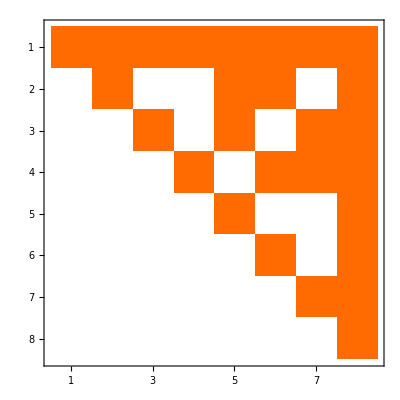

```mathematica
PseudoInverse[MobiusMatrixFromSets[Map[SymbolToSets,Sort[FindFullFormula[ReadGrof[4]],CompareSymbols]]]]//MatrixPlot
```

```mathematica
Table[If[i>j,0,If[i==j,1,Indexed[a,{i,j}]]],{i,6},{j,6}]//Inverse//MatrixForm
```

Inverse::matsq: Argument {{1,a,a,a,a,a},{0,1,a,a,a,a},{0,0,1,a,a,a},{0,0,0,1,a,a},{0,0,0,0,1,a}} at position 1 is not a non-empty square matrix.

Inverse[{{1,a12,a13,a14,a15,a16},{0,1,a23,a24,a25,a26},{0,0,1,a34,a35,a36},{0,0,0,1,a45,a46},{0,0,0,0,1,a56}}]

```mathematica
5
```

5

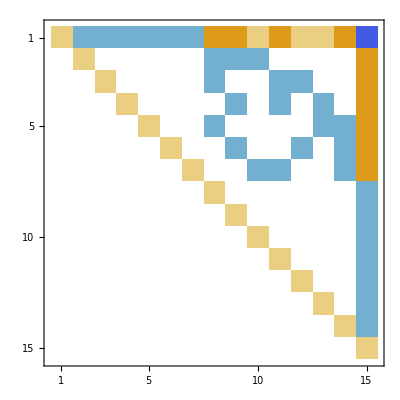

```mathematica
helper=MobiusMatrixFromSets[Map[SymbolToSets,Sort[FindFullFormula[Graph[Range[4],{}]],CompareSymbols]]];MatrixPlot[helper]
```

```mathematica
Det[Table[helper[[i,j]]*If[(i==j)||(i==1)||(j==Length[helper]),1,Indexed[a,{i,j}]],{i,Length[helper]},{j,Length[helper]}]]
```

1

```mathematica
Table[helper[[i,j]]*If[(i==j)||(i==1)||(j==Length[helper]),1,Indexed[a,{i,j}]],{i,Length[helper]},{j,Length[helper]}]//Inverse//MatrixForm
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | -2+a28+a38+a58 | -2+a29+a49+a69 | -1+a210+a710 | -2+a311+a411+a711 | -1+a312+a612 | -1+a413+a513 | -2+a514+a614+a714 | -17+a28+a29+a210+a38+a311+a312+a49+a411+a413+a58+a513+a514+a69+a612+a614+a710+a711+a714
0 | 1 | 0 | 0 | 0 | 0 | 0 | a28 | a29 | a210 | 0 | 0 | 0 | 0 | -2+a28+a29+a210
0 | 0 | 1 | 0 | 0 | 0 | 0 | a38 | 0 | 0 | a311 | a312 | 0 | 0 | -2+a38+a311+a312
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | a49 | 0 | a411 | 0 | a413 | 0 | -2+a49+a411+a413
0 | 0 | 0 | 0 | 1 | 0 | 0 | a58 | 0 | 0 | 0 | 0 | a513 | a514 | -2+a58+a513+a514
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | a69 | 0 | 0 | a612 | 0 | a614 | -2+a69+a612+a614
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | a710 | a711 | 0 | 0 | a714 | -2+a710+a711+a714
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1)

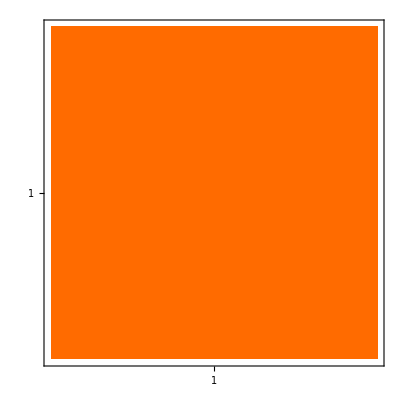

```mathematica
PseudoInverse[MobiusMatrixFromSets[Map[SymbolToSets,FindFullFormula[CompleteGraph[3]]]]]//MatrixPlot
```